VAJE 4

```mathematica
trikotnik = Trikotnik[{0,0}, {5,1}, {7,4}]
```

Trikotnik[{0,0},{5,1},{7,4}]

```mathematica
Stranice[{AA_, BB_, CC_}] := {{AA, BB}, {BB, CC}, {CC, AA}}
```

```mathematica
a = {{0,0}, {5,1}}
b = {{5,1}, {7,4}}
c = {{7,4}, {0,0}}
```

```mathematica
Stranice[{{0,0}, {5,1}, {7,4}}]
```

{{{0,0},{5,1}},{{5,1},{7,4}},{{7,4},{0,0}}}

```mathematica
Koti[Trikotnik[AA_,BB_,CC_]] := {Kot[CC, AA, BB], Kot[AA, BB, CC], Kot[BB, CC, AA] }
```

```mathematica
alfa = Kot[{7,4}, {0,0}, {5,1}]
```

```mathematica
Koti[Trikotnik[{0,0}, {5,1}, {7,4}]]
```

{Kot[{7,4},{0,0},{5,1}],Kot[{0,0},{5,1},{7,4}],Kot[{5,1},{7,4},{0,0}]}

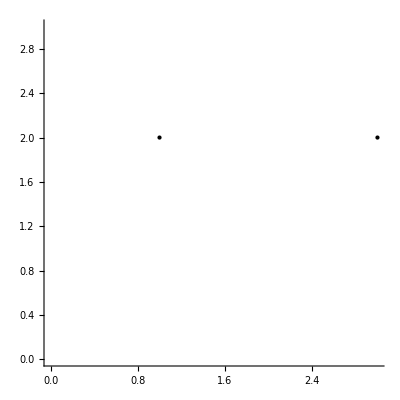

```mathematica
Graphics[{Point[{1,2}], Point[{3,2}]}, Axes -> True, PlotRange -> {{0,3},{0,3}}]
```

```mathematica
SlikaOglisc[Trikotnik[AA_,BB_,CC_]] := Graphics[{Point[AA], Point[BB], Point[CC]}]
```

```mathematica
SlikaOglisc[trikotnik]
```

-Graphics-

```mathematica
SlikaStranic[Trikotnik[AA_,BB_,CC_]] := Graphics[{Line[{AA, BB}], Line[{BB, CC}], Line[{CC, AA}]}]
```

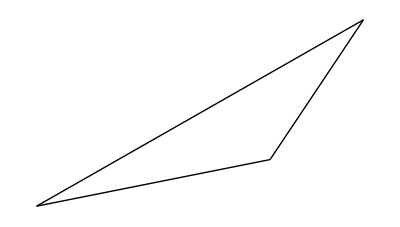

```mathematica
SlikaStranic[trikotnik]
```

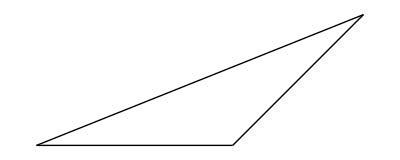

```mathematica
SlikaStranic[Trikotnik[{5,4},{3,2},{0,2}]]
```

```mathematica
ClearAll[NarisiTrikotnik]
```

```mathematica
NarisiTrikotnik[t_Trikotnik] := {SlikaOglisc[t], SlikaStranic[t]}
```

```mathematica
NarisiTrikotnik[trikotnik]
```

{-Graphics-,-Graphics-}

```mathematica
SlikaOglisc[Trikotnik[AA_,BB_,CC_]] := {Point[AA], Point[BB], Point[CC]}
SlikaStranic[Trikotnik[AA_,BB_,CC_]] := {Line[{AA, BB}], Line[{BB, CC}], Line[{CC, AA}]}
NarisiTrikotnik[t_Trikotnik] := Graphics[{SlikaOglisc[t], SlikaStranic[t]}]
```

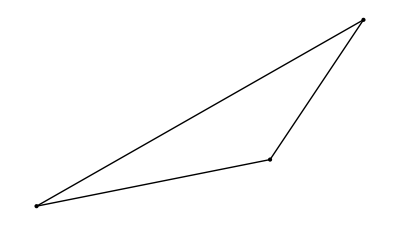

```mathematica
NarisiTrikotnik[trikotnik]
```